```mathematica
csvPath = "M:\\JI Courses\\Sophomore_Year\\2019_Spring\\VE401\\Proj2\\Figures\\2\\data.csv";
SystemOpen@csvPath
Data = Import[csvPath];
PosDate = Position[Data,"2019-01-01"];
AllDate = Data[[PosDate[[1,1]];;-1,PosDate[[1,2]];;PosDate[[1,2]]]];
For[i=1,i<=Length[AllDate],i++,AllDate[[i]]=DateObject[StringCases[AllDate[[i,1]],x:DatePattern[{"Year","Month","Day"}]:>DateList[x]][[1;;1,1;;3]]]];
Count1 = Tally[AllDate];
Count2 = Tally[Count1[[All,2]]]
```

{{1,14},{3,7},{5,5},{4,6},{2,9},{9,1}}

```mathematica
n=31+14;
NumZero = n;
For[i=1,i≤5,i++,NumZero = NumZero-Count2[[i,2]]];
Insert[Count2,{0,NumZero},1]
```

{{0,4},{1,14},{3,7},{5,5},{4,6},{2,9},{9,1}}

```mathematica
(*The fit done by Mathematica*)
Needs["HypothesisTesting`"];
TestData = Join[Table[0,{i,1,4}],Table[1,{i,1,14}],Table[2,{i,1,9}],Table[3,{i,1,7}],Table[4,{i,1,6}],Table[5,{i,1,5}],Table[9,{i,1,1}]];
PearsonChiSquareTest[TestData,PoissonDistribution[k1],{"FittedDistributionParameters","DegreesOfFreedom","TestDataTable"}]
```

{{k1→2.41304},3, | Statistic | P-Value
Pearson χ^2 | 3.09435 | 0.377305}

```mathematica
(*The fit done considering Pearson Criteria 3.1.2*)
Count2= {{0,4},{1,14},{2,9},{3,7},{4,6},{5,5},{9,1}};
k2 = 0;
For[i=1,i≤7,i++,k2 = k2+Count2[[i,1]]*Count2[[i,2]]];
k2 = N[k2/n]
```

2.46667

```mathematica
e= N[Exp[1]];
CRV={};
For[i=0,i≤5,i++,CRV =Insert[CRV,e^(-k2)*k2^i/Factorial[i],-1]];
Geq6=1;
For[i=1,i≤6,i++,Geq6= Geq6-CRV[[i]]];
CRV=Insert[CRV,Geq6,-1]
```

{0.0848673,0.209339,0.258185,0.212286,0.130909,0.064582,0.0398314}

```mathematica
ExpectedE = {};
For[i=1,i≤7,i++,ExpectedE =Insert[ExpectedE,n*CRV[[i]],-1]];
ExpectedE
```

{3.81903,9.42027,11.6183,9.55285,5.89092,2.90619,1.79241}

```mathematica
(*We see that the Pearson Criteria 3.1.2 is not satisfied, therefore we merge the last 2 categories and obtain the following*)
Count3 = {{0,4},{1,14},{2,9},{3,7},{4,6},{5,6}};
NewCRV={0.08486727897001742,0.20933928812604297,0.2581851220221197,0.21228554477374284,0.13090941927714142,0.0645819801767231+0.03983136665421254};
NewExpectedE={3.8190275536507836,9.420267965671933,11.618330490995385,9.552849514818428,5.890923867471364,2.9061891079525397+1.7924114994395641};
NewObservedE= {4,14,9,7,6,5+1};
(*The Degree of Fredom is found by*)
DegreesOfFreedom = Length[NewExpectedE]-1-1
```

4

```mathematica
(*The Pearson Statistic is found by*)
Stat = 0;
For[i=1,i≤6,i++,Stat=Stat+(NewObservedE[[i]]-NewExpectedE[[i]])^2/NewExpectedE[[i]]];
Stat
```

3.8698

```mathematica
(*Fix alpha=0.05, we test the null hypothesis, and fail to reject it*)
Solve[CDF[ChiSquareDistribution[DegreesOfFreedom],x]==0.95,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→9.48773}}

```mathematica
(*The P value is found by:*)
PValue = 1-CDF[ChiSquareDistribution[DegreesOfFreedom],Stat]
```

0.423913

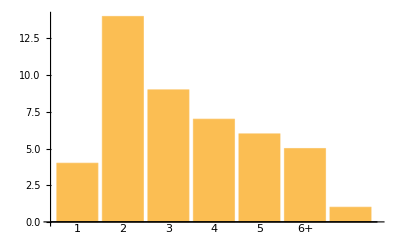

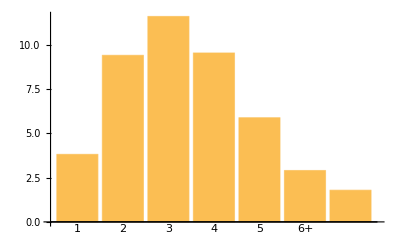

```mathematica
BarO= {4,14,9,7,6,5,1};
BarE= ExpectedE;
BarChart[BarO,ChartLabels->{"1","2","3","4","5","6+"}]
BarChart[BarE,ChartLabels->{"1","2","3","4","5","6+"}]
```